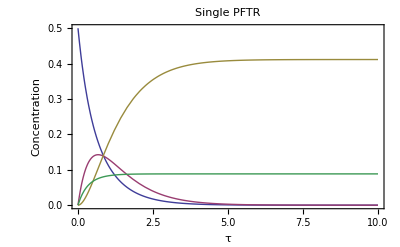

{0.142602,{t→0.671207}}

0.178254 m-xylene

0.103886 o-xylene

0.0752573 d

```mathematica
"SINGLE PFTR";
ClearAll["Global`"]
k1=1.2;
k2=1.5;
k3=1.1;

Solution1=NDSolve[{Ca'[t]==-k1*Ca[t]-k3*Ca[t]^2, Ca[0]==0.5}, Ca, {t,0,20}];
CaPFTR[t_]=Ca[t]/.Flatten[Solution1];
"Plot[CaPFTR[t], {t,0,20}, PlotRange→All]";

Solution2=NDSolve[{Cb'[t]==k1*CaPFTR[t]-k2*Cb[t],Cb[0]==0}, Cb, {t,0,20}];
CbPFTR[t_]=Cb[t]/.Flatten[Solution2];
"Plot[CbPFTR[t],{t,0,20}, PlotRange→All]";

Solution5=NDSolve[{Cc'[t]== k2*CbPFTR[t], Cc[0]== 0},Cc,{t,0,20}];
CcPFTR[t_]=Cc[t]/.Flatten[Solution5];

Solution4=NDSolve[{Cd'[t]==k3*CaPFTR[t]^2, Cd[0]==0}, Cd, {t,0,20}];
CdPFTR[t_]=Cd[t]/.Flatten[Solution4];
"Plot[CdPFTR[t],{t,0,20},PlotRange→All]";

Needs["PlotLegends`"];

Plot[{CaPFTR[t],CbPFTR[t],CcPFTR[t],CdPFTR[t]}, {t,0,10}, PlotLegend->{"m-xylene", "p-xylene", "o-xylene", "d"}, LegendPosition->{1.1,-0.4}, PlotRange->All,Frame->True, PlotStyle->{Thick}, PlotLabel->Style["Single PFTR",16],FrameLabel->{"τ","Concentration"}]

FindMaximum[CbPFTR[t],{t,0}]
"m-xylene" CaPFTR[0.6712070200182012]
"o-xylene" CcPFTR[0.6712070200182012]
"d" CdPFTR[0.6712070200182012]
```